# Pertołów

## Dane

### Nazwy plików konfiguracyjnych

```mathematica
(*fileg="configgLG";
*)
```

### Tensor metryczny

```mathematica
(*{g,x}=ReadList[fileg]*)
```

```mathematica
(* kowariantny tensor metryczny gμν - NALEŻY USTAWIĆ!; uwaga! numeracja w tabeli jest od 1 *)
(* wumiar przestrzeni: namx = liczba wierszy = liczba kolumn w tensorze metrycznym *)
nmax=4; 

(* longitudinal gauge, brak przestrzennych elementów pozadiagonalnych w tensorze energii-pędu, czas kosmiczny, zerowa krzywizna *)
g = Table[Which[ n == m && n==1, -(1+2*P*Φ[t,x1,x2,x3]),n == m && n==2, a[t]^2*(1-2*P*Φ[t,x1,x2,x3]),n == m && n==3, a[t]^2*(1-2*P*Φ[t,x1,x2,x3]),n == m && n==4, a[t]^2*(1-2*P*Φ[t,x1,x2,x3]), True , 0 ], {n , nmax } , {m , nmax }];
(*g = Table[Which[ n == m && n==1, -1,n == m && n==2, a[t]^2,n == m && n==3, a[t]^2,n == m && n==4, a[t]^2, True , 0 ], {n , nmax } , {m , nmax }];
*)
(* lista zmiennych, w których zapisana jest metryka - NALEŻY USTAWIĆ! *)
x={t,x1,x2,x3};
```

### Lagranżjan

```mathematica
(* liczba pól skalarnych N - NALEŻY USTAWIĆ! *)
lpol=1;

(* pomocniczy wektor z polami skalarnymi ϕ^I *)
(* nazwy pól - MOŻNA USTAWIĆ! (domyślnie ϕ1,ϕ2,...) *)
(*pola=Table[ToExpression["ϕ"<>ToString[I]],{I,1,lpol}]; *)
pola={ϕ};

(* metryka G w przestrzeni pól (tablica współczynników przy wyrazach z pochodnymi pól w lagranżjanie - zależą od pól) - więc tablica jest symetryczna *)
(* pola bez argumentów - NALEŻY USTAWIĆ! *)
(*fG=Table[If[I<=J,ToExpression["G"<>ToString[I]<>ToString[J]],ToExpression["G"<>ToString[J]<>ToString[I]]][Sequence@@pola],{I ,1,lpol } ,{J ,1,lpol }];*) 
fG=Table[Which[ I == J && I==1, 1, True , 0 ],{I ,1,lpol } ,{J ,1,lpol }];

(* lagranżjan z artykułu arXiv:0801.1085v2 L=P(X,pola) *)
(* pola bez argumentów i ogólnie zapisany człon kinetyczny XK, jeżeli potencjał jest wpisywany ogólnie to wstawiamy V[Sequence@@pola] - NALEŻY USTAWIĆ! *)
(*La=fP[XK,Sequence@@pola]; *)
La=XK-V[Sequence@@pola];

(* funkcje i parametry, występujące w lagranżjanie - NALEŻY USTAWIĆ! *)
fun={V->(((Subscript[m, ϕ]*#1)^2)/2 &)};
param=Rationalize[{Subscript[m, ϕ]->10^-7}];
(*param={mϕχ->1/7,γ->0};*)
(*fun={V->(V0+V1*Sqrt[(#1^4)^(1/3)]*Exp[-2*β1*(#1^4)^(1/3)]+V2*(#1^4)^(1/3)*Exp[-β1*(#1^4)^(1/3)]*Cos[β2*#2]&),b->(b0-Log[#1]/3 &)};
param={V0->9.*10^(-14),V1->3.2*10^(-4),β1->9.4*10^5,V2->1.1*10^(-5),β2->2*Pi/3,b0->-11};*)

(* grawitacyjna część lagranżjanu w teorii f(R) (domyślnie f(R)=R), skalar Ricciego musi być oznaczony przez rr[Sequence@@pola] - NALEŻY USTAWIĆ *)
fR=rr[Sequence@@x];

(* nazwa tworzonego pliku z równaniami - NALEŻY USTAWIĆ! *)
sciezka="C:\\Users\\user\\Documents\\doktorat\\doktorat\\wyniki";
nazwaplikurow="1pole";
```

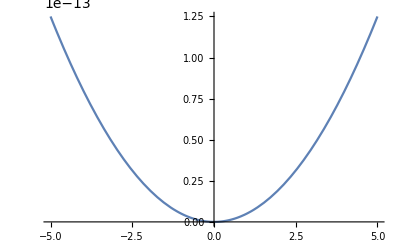

```mathematica
VT[x1_]:=V[x1] /.fun /. param 
Plot[VT[xx],{xx,-5,5}]
```

## Program

```mathematica
(* wyłączenie komunikatów o użyciu funkcji Inverse przez Solve *)
Off[Solve::ifun];
(* wyłączenie komunikatów o rozwiązywaniu równań algebraicznych i różniczkowych *)
Off[NDSolve::pdord];
```

```mathematica
Needs["mrkFasadaPertolow`"]
```

### Równania

```mathematica
Block[{ruchurow0,polarow000,ruchurow1,polarow001,polarow011,rowMS1,Ebaza,rowKI1,rowu1,wpisNb,wpisR,wpisB},(
(* równania dla tła *)
ruchurow0=RuchuRownaniakw[g,x,pola,fG,La,0];
polarow000=PolaRownaniekw[pola,fG,La,fR,0,0,g,x,0];
(* równania dla liniowych perturbacji *)
ruchurow1=Simplify[RuchuRownaniakw[g,x,pola,fG,La,1]];
polarow001=PolaRownaniekw[pola,fG,La,fR,0,0,g,x,1];
polarow011=PolaRownaniekw[pola,fG,La,fR,0,1,g,x,1];
(* równania dla zmiennych Mukhanova-Sasakiego *)
rowMS1=MukhanovSasakiRownaniakw[pola,fG,La,g,x,fR,1];
(* baza Freneta *)
Ebaza=BazaFreneta[g,x,pola,fG,La];
(* równania dla zmiennych krzywizny i izokrzywizny *)
rowKI1=TimeConstrained[PerturbacjeAERownaniakw[pola,fG,La,g,x,fR,True,1,True],0,{}];

(* równania dla zmiennych współporuszających się *)
rowu1=WspolporuszajaceRownaniakw[pola,fG,La,g,x,fR,True,1,True];

(* zapisanie wyników do notebooka *)
wpisNb={{"Równania ruchu tła",ruchurow0},{"Równanie pola 00 dla tła",polarow000},{"Równania ruchu dla liniowych perturbacji",ruchurow1},{"Równanie pola 00 dla liniowych perturbacji",polarow001},{"Równanie pola 01 dla liniowych perturbacji",polarow011},{"Równania dla zmiennych Mukhanova-Sasakiego",rowMS1},{"Baza Freneta",Ebaza},{"Równania dla zmiennych krzywizny i izokrzywizny",rowKI1},{"Równania dla zmiennych współporuszających się",rowu1}};
PlikNb[wpisNb,nazwaplikurow,sciezka];
(* zapisanie równań w formie latexowej do pliku txt *)
wpisR={{"Równania ruchu tła",ruchurow0},{"Równanie pola 00 dla tła",polarow000},{"Równania ruchu dla liniowych perturbacji",ruchurow1},{"Równanie pola 00 dla liniowych perturbacji",polarow001},{"Równanie pola 01 dla liniowych perturbacji",polarow011},{"Równania dla zmiennych Mukhanova-Sasakiego",rowMS1},{"Równania dla zmiennych krzywizny i izokrzywizny",rowKI1},{"Równania dla zmiennych współporuszających się",rowu1}};
PlikTexRownania[pola,wpisR,nazwaplikurow,sciezka];
(* zapisanie bazy w formie latexowej do pliku txt *)
wpisB={"Baza Freneta",Ebaza};
PlikTexBaza[pola,wpisB,nazwaplikurow,sciezka];
)]//AbsoluteTiming
```

01:29:53GMT+2.TimeObject[{1,29,53.8012},TimeZone→2.] Równania ruchu w rzędzie 0

01:29:54GMT+2.TimeObject[{1,29,54.5043},TimeZone→2.] Równanie pola 00 w rzędzie 0

01:29:54GMT+2.TimeObject[{1,29,54.7075},TimeZone→2.] Równania ruchu w rzędzie 1

01:29:54GMT+2.TimeObject[{1,29,54.7856},TimeZone→2.] Równanie pola 00 w rzędzie 1

01:29:54GMT+2.TimeObject[{1,29,54.8949},TimeZone→2.] Równanie pola 01 w rzędzie 1

01:29:54GMT+2.TimeObject[{1,29,54.9418},TimeZone→2.] Równanie pola 11 w rzędzie 0

01:29:54GMT+2.TimeObject[{1,29,54.9887},TimeZone→2.] Baza Freneta

Det::matsq: Argument {{{ϕ'[t]/(√(ϕ'[t]^2))}}} at position 1 is not a non-empty square matrix.

TimeConstrained::timc: Number of seconds 0 is not a positive machine-sized number or Infinity.

01:29:55GMT+2.TimeObject[{1,29,55.0668},TimeZone→2.] Równania ruchu dla zmiennych współporuszających się

{1.85142,Null}

```mathematica
g = Table[Which[ n == m && n==1, -1,n == m && n==2, a[t]^2,n == m && n==3, a[t]^2,n == m && n==4, a[t]^2, True , 0 ], {n , nmax } , {m , nmax }];
Block[{ruchurow0,polarow000,ruchurow1,polarow001,polarow011,Ebaza,rowKI1,rowu1,wpisNb,wpisR,wpisB},(
(* równania dla tła *)
ruchurow0=RuchuRownaniakw[g,x,pola,fG,La,0];
polarow000=PolaRownaniekw[pola,fG,La,fR,0,0,g,x,0];
(* równania dla liniowych perturbacji *)
ruchurow1=Simplify[RuchuRownaniakw[g,x,pola,fG,La,1]];
polarow001=PolaRownaniekw[pola,fG,La,fR,0,0,g,x,1];
polarow011=PolaRownaniekw[pola,fG,La,fR,0,1,g,x,1];
(* baza Freneta *)
Ebaza=BazaFreneta[g,x,pola,fG,La];
(* równania dla zmiennych krzywizny i izokrzywizny *)
rowKI1=TimeConstrained[PerturbacjeAERownaniakw[pola,fG,La,g,x,fR,False,1,True],60,{}];
(* równania dla zmiennych współporuszających się *)
rowu1=WspolporuszajaceRownaniakw[pola,fG,La,g,x,fR,False,1,True];
(* zapisanie wyników do notebooka *)
wpisNb={{"Równania ruchu tła",ruchurow0},{"Równanie pola 00 dla tła",polarow000},{"Równania ruchu dla liniowych perturbacji",ruchurow1},{"Równanie pola 00 dla liniowych perturbacji",polarow001},{"Równanie pola 01 dla liniowych perturbacji",polarow011},{"Baza Freneta",Ebaza},{"Równania dla zmiennych krzywizny i izokrzywizny",rowKI1},{"Równania dla zmiennych współporuszających się",rowu1}};
PlikNb[wpisNb,nazwaplikurow,sciezka];
(* zapisanie równań w formie latexowej do pliku txt *)
wpisR={{"Równania ruchu tła",ruchurow0},{"Równanie pola 00 dla tła",polarow000},{"Równania ruchu dla liniowych perturbacji",ruchurow1},{"Równanie pola 00 dla liniowych perturbacji",polarow001},{"Równanie pola 01 dla liniowych perturbacji",polarow011},{"Równania dla zmiennych krzywizny i izokrzywizny",rowKI1}};
PlikTexRownania[pola,wpisR,nazwaplikurow,sciezka];
(* zapisanie bazy w formie latexowej do pliku txt *)
wpisB={"Baza Freneta",Ebaza};
PlikTexBaza[pola,wpisB,nazwaplikurow,sciezka];
)]//AbsoluteTiming
```

18:07:01GMT+2.TimeObject[{18,7,1.04216},TimeZone→2.] Równania ruchu w rzędzie 0

18:07:01GMT+2.TimeObject[{18,7,1.15805},TimeZone→2.] Równania ruchu w rzędzie 0

18:07:01GMT+2.TimeObject[{18,7,1.27394},TimeZone→2.] Równanie pola 00 w rzędzie 0

18:07:01GMT+2.TimeObject[{18,7,1.32733},TimeZone→2.] Równania ruchu w rzędzie 1

18:07:01GMT+2.TimeObject[{18,7,1.32733},TimeZone→2.] Równania ruchu w rzędzie 1

18:07:01GMT+2.TimeObject[{18,7,1.38071},TimeZone→2.] Równanie pola 00 w rzędzie 1

18:07:01GMT+2.TimeObject[{18,7,1.39635},TimeZone→2.] Równanie pola 01 w rzędzie 1

18:07:01GMT+2.TimeObject[{18,7,1.41196},TimeZone→2.] Baza Freneta

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve::svars will be suppressed during this calculation.

18:07:01GMT+2.TimeObject[{18,7,1.72756},TimeZone→2.] Równania ruchu dla składowych krzywizny i izokrzywizny

18:07:02GMT+2.TimeObject[{18,7,2.88199},TimeZone→2.] Równania ruchu dla zmiennych współporuszających się

{2.26458,Null}

### Wartości początkowe

```mathematica
Print[TimeObject[Now]];
{tloi,Ntot, tf}=Block[{wstepneWP,wstepneWSP,Nall},(
(* szukanie wartości początkowych *)
(* liczba e-powiększeń, N(0) ustawione jest na -8 - NALEŻY USTAWIĆ! *)
Nall=68.;
(* wstępne wartości początkowe i współczynniki - NALEŻY USTAWIĆ! *)
wstepneWP={16.42};
wstepneWSP={0.01};
(*wstepneWP={11.60,11.60};
wstepneWSP={0.01,0.01};*)
WartosciPoczatkoweTlo[pola,fG,La,g,x,fR,Nall,wstepneWP,wstepneWSP,fun,param])]
```

01:30:01GMT+2.TimeObject[{1,30,1.59814},TimeZone→2.]

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{ϕ[0.]==16.42,ϕ'[0.]==-8.16497×10^-8,nn[0.]==0.}

67.9735

{{{16.42},{0.}},67.973,1.91406×10^8}

```mathematica
(* początkowa wartość liczby e-powiększeń dla tła (N0t) i perturbacji (N0p) - NALEŻY USTAWIĆ! *)
N0t=-8.;
N0p=-8.;
```

### Tło

```mathematica
(* efektywna prędkość dźwięku *)
PredkoscDzwiekuEf[g,x,pola,fG,La]
```

1

```mathematica
(* trajektorie inflacyjne w przestrzeni pól *)
Print[TimeObject[Now]];
TrajektorieTlo[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t];//AbsoluteTiming
```

01:30:08GMT+2.TimeObject[{1,30,8.95872},TimeZone→2.]

01:30:08GMT+2.TimeObject[{1,30,8.95872},TimeZone→2.] Rozwiązania dla tła

01:30:09GMT+2.TimeObject[{1,30,9.09934},TimeZone→2.] Liczba e-powiększeń

01:30:09GMT+2.TimeObject[{1,30,9.09934},TimeZone→2.] Czasy

01:30:09GMT+2.TimeObject[{1,30,9.91187},TimeZone→2.] Epilog

01:30:09GMT+2.TimeObject[{1,30,9.91187},TimeZone→2.] Wykres

{1.46739,Null}

```mathematica
(*(* trajektorie inflacyjne w przestrzeni pól *)
Print[TimeObject[Now]];
TrajektorieTlo[pola,fG,La,g,x,fR,wartpocz[[2,1]],wartpocz[[2,3]]+0.2*wartpocz[[2,3]],fun,param,sciezka];//AbsoluteTiming*)
```

```mathematica
(* pochodne pól w zależności od liczby e-powiększeń *)
PochodnePol[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t];//AbsoluteTiming
```

22:51:34GMT+2.TimeObject[{22,51,34.9843},TimeZone→2.] Liczba e-powiększeń

22:51:34GMT+2.TimeObject[{22,51,34.9843},TimeZone→2.] Wykres 1

22:51:35GMT+2.TimeObject[{22,51,35.3007},TimeZone→2.] Wykres 2

{0.620838,Null}

```mathematica
Test 
(* czas kosmiczny dla danej liczby e-powiększeń *)
Block[{testN},(testN=0.1;
CzasN[testN,pola,fG,La,g,x,fR,tloi,tf,fun,param,N0t])]
```

Test

1.5331261199999999865895

```mathematica
(* prędkości kątowe, parametryzujące ewolucję czasową bazy Freneta, w zależności od liczby e-powiększeń *)
PredkosciKatoweBazy[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t];//AbsoluteTiming
```

{-0.000389815,{t→0.5}}

22:51:41GMT+2.TimeObject[{22,51,41.7618},TimeZone→2.] Liczba e-powiększeń i zmienne

22:51:41GMT+2.TimeObject[{22,51,41.7618},TimeZone→2.] Wykres

{1.04297,Null}

```mathematica
(* kwadraty mas w zależności od liczby e-powiększeń *)
Masy[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t];//AbsoluteTiming
```

01:31:09GMT+2.TimeObject[{1,31,9.59993},TimeZone→2.] Liczba e-powiększeń i masy

01:31:09GMT+2.TimeObject[{1,31,9.59993},TimeZone→2.] Wykres

{0.774031,Null}

```mathematica
(* kwadraty efektywnych mas w zależności od liczby e-powiększeń (po przejściu do bazy Freneta dla zakrzywionych trajektorii) *)
MasyEfektywne[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t];//AbsoluteTiming
```

23:21:09GMT+2.TimeObject[{23,21,9.46666},TimeZone→2.] Macierz masy w bazie Freneta

23:21:09GMT+2.TimeObject[{23,21,9.46666},TimeZone→2.] Efektywna macierz masy

23:21:09GMT+2.TimeObject[{23,21,9.48227},TimeZone→2.] Liczba e-powiększeń i masy

23:21:09GMT+2.TimeObject[{23,21,9.48227},TimeZone→2.] Wykres

{1.4026,Null}

```mathematica
Test 
(* wartości bazy wektorów własnych macierzy masy dla pierwotnych pól i bazy Freneta w danej chwili t *)
Block[{testt,bm,bf},(testt=tf;
bm=BazaMasyTest[testt,pola,fG,La,g,x,fR,tloi,tf,fun,param,N0t];
Print[bm];
bf=BazaFrenetaTest[testt,pola,fG,La,g,x,fR,tloi,tf,fun,param,N0t];
 Print[bf];)]
```

Test

Macierz masy: {{0.494,0},{0,1.}}

Wartości własne macierzy masy: {0.494,1.}

{{1.,0},{0,0.74593}}

{{0.046795,-0.74511},{0.9989,0.034906}}

k_turn: 9.95×10^-6 ; k(N=3.)=0.0002: {0.000285,0.0028,0.0159}

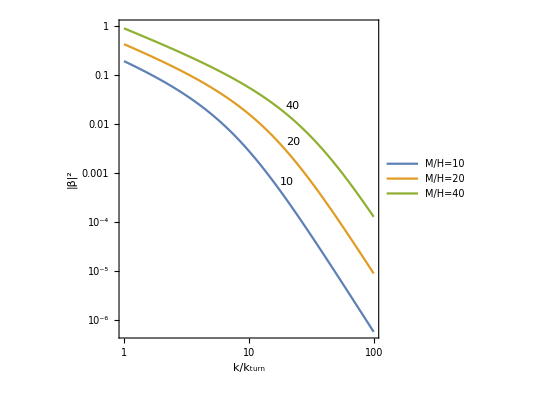

```mathematica
(* liczba obsadzeń w uproszczonej wersji *)
Block[{ml={Subscript[m, ϕ]},mh={M*Cos[Δθ/2]}, kwT,kw, Nkw, r,lo,oznaczenia,legenda},(Nkw=3.;
ml={10^(-7),10^(-7),10^(-7)};mh={10^(-4),2*10^(-4),4*10^(-4)}*Cos[Δθ/2];
(*ml=Sqrt[{7.76299765758533512252288`3.*^-15,7.78304813674637556616972`3.*^-15,7.85564992125592731739564`3.*^-15}];
Print[SetPrecision[ml,3]];
mh=Sqrt[{1.257749211116955634518400516125`3.*^-8,5.030996171265834105472520929898`3.*^-8,2.0123984011201655904553735344481`3.*^-7}];
Print[SetPrecision[mh,3]];*)

{kwT,kw}=Take[WektorFalowyTest[Nkw,pola,fG,La,g,x,fR,tloi,tf,fun,param,N0t],2];

r=MapThread[Sqrt[(kw^2+#2^2)/(kw^2+#1^2)] &,{ml,mh}];
Print["k_turn: ",SetPrecision[kwT,3]," ; k(N=",Nkw,")=",SetPrecision[kw,3],": ",SetPrecision[(((Sqrt[r]-1/Sqrt[r])Sin[Δθ])^2)/4 /. param,3]];
lo=Function[{k,ml,mh},(((Sqrt[Sqrt[(k^2+mh^2)/(k^2+ml^2)]]-1/Sqrt[Sqrt[(k^2+mh^2)/(k^2+ml^2)]])Sin[Δθ])^2)/4 /. param];

oznaczenia={10,20,40};
legenda=Map["StyleBox[\"M\",\nFontSlant->\"Italic\"]/StyleBox[\"H\",\nFontSlant->\"Italic\"]="<>ToString[#] &,oznaczenia];
LogLogPlot[Evaluate[MapThread[Labeled[lo[k*kwT,ml[[#1]],mh[[#1]]],#2,{Scaled[0.5],Above}] &, {Range[Length[oznaczenia]],oznaczenia}]],{k,1,1*10^2},Frame->True, AspectRatio->1, FrameLabel->{"StyleBox[\"k\",\nFontSlant->\"Italic\"]/SubscriptBox[ StyleBox[\"k\",\nFontSlant->\"Italic\"], \"turn\"]","|β|^2"},PlotLegends->Placed[legenda,{Left,Bottom}]]
)]
```

```mathematica
(* wykresy elementów bazy wektorów własnych macierzy masy *)
WykresyBazaMasy[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t];//AbsoluteTiming
```

21:50:00GMT+2.TimeObject[{21,50,0.0850189},TimeZone→2.] Liczba e-powiększeń i baza wektorów własnych macierzy masy

21:50:00GMT+2.TimeObject[{21,50,0.0850189},TimeZone→2.] Wykres wierszy 1

21:50:02GMT+2.TimeObject[{21,50,2.57434},TimeZone→2.] Wykres wierszy 2

21:50:04GMT+2.TimeObject[{21,50,4.5401},TimeZone→2.] Wykres kolumn 1

21:50:06GMT+2.TimeObject[{21,50,6.54504},TimeZone→2.] Wykres kolumn 2

{8.50516,Null}

```mathematica
(* wykresy elementów bazy Freneta *)
WykresyBaza[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t];//AbsoluteTiming
```

23:30:27GMT+2.TimeObject[{23,30,27.6127},TimeZone→2.] Baza wektorów własnych macierzy masy

23:30:27GMT+2.TimeObject[{23,30,27.769},TimeZone→2.] Liczba e-powiększeń i baza

23:30:27GMT+2.TimeObject[{23,30,27.7846},TimeZone→2.] Wykres wierszy 1

23:30:28GMT+2.TimeObject[{23,30,28.3628},TimeZone→2.] Wykres wierszy 2

23:30:28GMT+2.TimeObject[{23,30,28.894},TimeZone→2.] Wykres kolumn 1

Part::partd: Part specification {0.0105455,0.0327563}⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification {0.0095643,0.0349059}⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

23:30:29GMT+2.TimeObject[{23,30,29.4409},TimeZone→2.] Wykres kolumn 2

{2.16967,Null}

```mathematica
Test 
(* wykresy funkcji zależnych od pól i liczby e-powiększeń oraz ich pierwszych pochodnych w zależności od liczby e-powiększeń *)
Block[{funkcje,opisy,rozwiazania0,Ebaza,dd,Lao,Go,Xo,ddϕN0,rownaniaNkw,rownaniaPkw,pertkw},(
(*funkcje={Map[#'[x[[1]]]/Symbol["nn"]'[x[[1]]] &, pola]};
opisy={{"wkladPM",Map[ToString[#]<>"'(t)/H" &, pola]}};*)

(*funkcje=Abs[Simplify[WspolczynnikiOddzialywaniaAE[pola,fG,La,g,x,fR,False]/.{H->Symbol["nn"]'}]]+10.^(-6);
opisy={{"Cσ",{"C_σs1"}},{"Cs1",{"C_s1σ"}}};*)

(*funkcje={{(5*10^(-4)/(Symbol["nn"]'[x[[1]]]))}};
opisy={{"MH",{"M/H"}}};*)

funkcje={{Symbol["nn"]'[x[[1]]]}};
opisy={{"H",{"H"}}};

funkcje={{Sqrt[7.78393150738920391080495`3.*^-15]*Exp[Symbol["nn"][x[[1]]]],Sqrt[5.0309961713836544599456755437`3.*^-8]*Exp[Symbol["nn"][x[[1]]]]}};
opisy={{"am2",{"ml","mh"}}};

Lao=Take[mrkLagrange`lagrangianO[g,x,pola,fG,La],{4}][[1]]/. Symbol["P"]->0;

dd=- ((Symbol["nn"][x[[1]]]*Symbol["nn"]'[x[[1]]]*Exp[Symbol["nn"][x[[1]]]])^2 - Exp[2*Symbol["nn"][x[[1]]]] * (Symbol["nn"]'[x[[1]]]^2 + (Lao)))/2;

funkcje={{7.78393150738920391080495`3.*^-15*Exp[2*Symbol["nn"][x[[1]]]]+dd,5.0309961713836544599456755437`3.*^-8*Exp[2*Symbol["nn"][x[[1]]]]+dd}};
opisy={{"am2_dda",{"ml","mh"}}};

(*funkcje=Abs[{{(Symbol["nn"][x[[1]]]*Symbol["nn"]'[x[[1]]]*Exp[Symbol["nn"][x[[1]]]])^2 ,-Exp[2*Symbol["nn"][x[[1]]]] * ((Symbol["nn"]'[x[[1]]])^2+ (Xo )), (Symbol["V"])}}];
opisy={{"dda",{"da2","dda","La"}}};*)

(*funkcje={{7.78393150738920391080495`3.*^-15*Exp[2*Symbol["nn"][x[[1]]]],5.0309961713836544599456755437`3.*^-8*Exp[2*Symbol["nn"][x[[1]]]]}};
opisy={{"am2",{"ml","mh"}}};*)

(*funkcje={{Exp[Symbol["nn"][x[[1]]]]}};
opisy={{"a",{"a"}}};*)



(* tensor metryczny w przestrzeni pól z polami podzielonymi na tło i perturbacje oraz człon kinetyczny *)
{Go,Xo}=Take[mrkLagrange`lagrangianO[g,x,pola,fG,La],{2,3}]/.{Symbol["P"]->0};
(* rozwiązania równań dla tła dla danych wartości początkowych *)
rozwiazania0=mrkFasadaPertolow`Private`RozwiazanieTlo[pola,fG,La,g,x,fR,N0t,tloi,tf,fun,param];
(* ========== zrobić mechanizm też dla innej bazy ============= *)
(* baza Freneta - ortonormalna baza w przestrzeni pól zorientowana kanonicznie *)
Ebaza=BazaFreneta[g,x,pola,fG,La];
Ebaza=mrkLagrange`bazaMasy[g,x,pola,fG,La][[2]];
(* lista podstawień drugich pochodnych pierwotnych pól wyznaczonych z równań ruchu dla tła *)
dd=mrkFasadaPertolow`Private`ddpolaN0f[g,x,pola,fG,La];
(* ======= do równań dla pierwotnych pól należy dodać jeszcze coś na perturbację metryki????? ============== *)
(* równania ruchu dla składowych fourierowskich pierwotnych/MS zmiennych *)
rownaniaNkw=MukhanovSasakiRownaniakw[pola,fG,La,g,x,fR,1];
(* równania ruchu dla składowych fourierowskich zmiennych adiabatycznej i entropowych *)
{rownaniaPkw,pertkw}={mrkIzoKrzywizna`ruchuRNAEkwO[pola,Go,Ebaza,x,rownaniaNkw,dd,True,1] /. fun /. param, mrkIzoKrzywizna`perturbacjeRSkw[pola,True]};
(*funkcje=Sqrt[{(-(mrkUzyteczny`wspolczynnikiRow[rownaniaPkw[[1]],{pertkw[[1]]''[x[[1]]]},{pertkw[[2]]'[x[[1]]]}]/2)+pola[[2]]'[x[[1]]]*Exp[-pola[[1]][x[[1]]]])/Symbol["nn"]'[x[[1]]]/.{H->Symbol["nn"]',Symbol["a"][x[[1]]]->Exp[Symbol["nn"][x[[1]]]]}}^2];*)
funkcje=Sqrt[{(-(mrkUzyteczny`wspolczynnikiRow[rownaniaPkw[[1]],{pertkw[[1]]''[x[[1]]]},{pertkw[[2]]'[x[[1]]]}]/2))/Symbol["nn"]'[x[[1]]]/.{H->Symbol["nn"]',Symbol["a"][x[[1]]]->Exp[Symbol["nn"][x[[1]]]]}}^2];
(*Print[funkcje];*)
opisy={{"wsp_teta",{"dt/H"}}};


WykresyTestoweTlo[funkcje,opisy,pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t];)]//AbsoluteTiming
```

Test

23:10:55GMT+2.TimeObject[{23,10,55.2887},TimeZone→2.] Baza wektorów własnych macierzy masy

Simplify::time: Time spent on a transformation exceeded 5. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

23:14:12GMT+2.TimeObject[{23,14,12.6657},TimeZone→2.] Równania ruchu dla składowych krzywizny i izokrzywizny

$Aborted

### Perturbacje

```mathematica
(* widma *)
Print[TimeObject[Now]];
Widma[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->True,Nkw->0.];//AbsoluteTiming
```

01:34:16GMT+2.TimeObject[{1,34,16.9299},TimeZone→2.]

01:34:16GMT+2.TimeObject[{1,34,16.9299},TimeZone→2.] Liczba e-powiększeń i widma

01:34:16GMT+2.TimeObject[{1,34,16.9299},TimeZone→2.] Wykres

01:34:17GMT+2.TimeObject[{1,34,17.7737},TimeZone→2.] Liczba e-powiększeń i widma

01:34:17GMT+2.TimeObject[{1,34,17.7737},TimeZone→2.] Wykres wierszy 1

01:34:18GMT+2.TimeObject[{1,34,18.2424},TimeZone→2.] Wykres kolumn 1

{1.78262,Null}

```mathematica
Print[TimeObject[Now]];
WidmaMB[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->True,Nkw->3.];//AbsoluteTiming
```

22:40:19GMT+2.TimeObject[{22,40,19.4566},TimeZone→2.]

22:40:19GMT+2.TimeObject[{22,40,19.4722},TimeZone→2.] Rozwiązania dla perturbacji

22:40:21GMT+2.TimeObject[{22,40,21.3462},TimeZone→2.] Liczba e-powiększeń i widma

22:40:21GMT+2.TimeObject[{22,40,21.3462},TimeZone→2.] Wykres

22:41:21GMT+2.TimeObject[{22,41,21.5195},TimeZone→2.] Wykres wierszy 1

22:42:01GMT+2.TimeObject[{22,42,1.89663},TimeZone→2.] Wykres wierszy 2

22:43:37GMT+2.TimeObject[{22,43,37.0677},TimeZone→2.] Wykres kolumn 1

$Aborted

```mathematica
Print[TimeObject[Now]];
Widmak[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->True,Nkw->0.];//AbsoluteTiming
```

02:10:54GMT+2.TimeObject[{2,10,54.3435},TimeZone→2.]

02:10:54GMT+2.TimeObject[{2,10,54.3591},TimeZone→2.] Rozwiązania dla perturbacji

02:10:54GMT+2.TimeObject[{2,10,54.3591},TimeZone→2.] Perturbacje ℛ i 𝒮

02:10:54GMT+2.TimeObject[{2,10,54.3591},TimeZone→2.] Widma

02:10:54GMT+2.TimeObject[{2,10,54.3591},TimeZone→2.] Widma

{t→8.40846024210962985336781×10^6}

1

{t→1.57488756822394797253609×10^7}

1

6.12837×10^-13

1.54237×10^-10

4.9328×10^-15

02:11:47GMT+2.TimeObject[{2,11,47.6096},TimeZone→2.] Wykres

$Aborted

```mathematica
Test 
(* widma dla podanej bazy *)
Print[TimeObject[Now]];
Block[{baza},(
baza={};
baza={{1,0,0},{0,1,0},{0,0,1}};
WidmaTest[baza,pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p];)]//AbsoluteTiming
```

16:15:53GMT+2.TimeObject[{16,15,53.1763},TimeZone→2.]

16:15:53GMT+2.TimeObject[{16,15,53.1919},TimeZone→2.] Perturbacje ℛ i 𝒮

16:15:54GMT+2.TimeObject[{16,15,54.8795},TimeZone→2.] Widma

16:15:55GMT+2.TimeObject[{16,15,55.0357},TimeZone→2.] Liczba e-powiększeń i widma

16:15:55GMT+2.TimeObject[{16,15,55.2857},TimeZone→2.] Wykres

{4.00844,Null}

```mathematica
(* korelacje względne *)
Print[TimeObject[Now]];
KorelacjeWzgledne[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->False,Nkw->3.];//AbsoluteTiming
```

19:56:40GMT+2.TimeObject[{19,56,40.3111},TimeZone→2.]

19:56:40GMT+2.TimeObject[{19,56,40.8631},TimeZone→2.] Rozwiązania dla tła

19:56:42GMT+2.TimeObject[{19,56,42.2924},TimeZone→2.] Rozwiązania dla tła

19:56:43GMT+2.TimeObject[{19,56,43.7157},TimeZone→2.] Rozwiązania dla tła

19:56:46GMT+2.TimeObject[{19,56,46.1619},TimeZone→2.] Rozwiązania dla perturbacji

19:56:50GMT+2.TimeObject[{19,56,50.8454},TimeZone→2.] Korelacje

19:56:50GMT+2.TimeObject[{19,56,50.8464},TimeZone→2.] Korelacje względne

19:56:51GMT+2.TimeObject[{19,56,51.8383},TimeZone→2.] Liczba e-powiększeń i względne korelacje

19:56:51GMT+2.TimeObject[{19,56,51.8403},TimeZone→2.] Wykres

{13.2693,Null}

```mathematica
(*Print[TimeObject[Now]];
Korelacje[pola,fG,La,g,x,fR,wartpocz[[2,1]],wartpocz[[2,3]],fun,param,sciezka,N0->N0t, N0P->N0p];//AbsoluteTiming*)
```

```mathematica
Test
(* liczby falowe dla N=0 (k1) i N=Nkw (k2) w momencie przekraczania promienia Hubble'a: k=aH; {k1, k2, k1-k2} *)
Block[{Nkw},(Nkw=0.1;
WektorFalowyTest[Nkw,pola,fG,La,g,x,fR,tloi,tf,fun,param,N0t])]
```

Test

21:10:04GMT+2.TimeObject[{21,10,4.6122},TimeZone→2.] Rozwiązania dla tła

{9.951326515678865656745×10^-6,0.0000109979171717230434808,-1.046590656044177824×10^-6}

```mathematica
(* produkcja cząstek *)
Print[TimeObject[Now]];
LiczbaObsadzenN[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->True,Nkw->3.];//AbsoluteTiming
```

05:53:31GMT+2.TimeObject[{5,53,31.823},TimeZone→2.]

05:53:32GMT+2.TimeObject[{5,53,32.8944},TimeZone→2.] Rozwiązania dla perturbacji

05:53:33GMT+2.TimeObject[{5,53,33.2265},TimeZone→2.] Baza wektorów własnych macierzy masy

05:53:33GMT+2.TimeObject[{5,53,33.8963},TimeZone→2.] Perturbacje w nowej bazie

05:53:59GMT+2.TimeObject[{5,53,59.5688},TimeZone→2.] Liczba e-powiększeń i liczby obsadzeń

0.00698337

05:54:11GMT+2.TimeObject[{5,54,11.1488},TimeZone→2.] Wykres

{16939.,Null}

```mathematica
(* indeksy spektralne dla perturbacji oraz wzmocnienie perturbacji krzywizny *)
Block[{Nk=0.1,k1,k2,dk,indeksns,PRf,opisy,wartosci,nazwaplikuwp},(
(* liczby falowe i indeksy spektralne *)
{k1,k2,dk,indeksns}=IndeksSpektralny[pola,fG,La,g,x,fR,tloi,tf,fun,param,N0->N0t, N0P->N0p,Nkw2->Nk,MS->False];
(* wzmocnienie perturbacji krzywizny *)
PRf=Wzmocnienie[pola,fG,La,g,x,fR,tloi,tf,fun,param,N0->N0t, N0P->N0p,MS->False];
(* zapisanie wyników *)
opisy=Join[ Map[#[[1]] &, param], {Subscript[N,"0t"],Subscript[N,"0p"],Subscript[N,"tot"]}, Map[Subscript[#,0]&, pola], Map[Subscript[OverDot[#],0]&, pola], {Subscript[k,0],Subscript[k,Nk],Δ k}, {Subscript[n,"s"](Subscript[P,ℛ])},Map[Subscript[n,"s"](Subscript[P,Subscript[𝒮,#]]) &, Range[lpol-1]], {λ}];
wartosci=Flatten[{Map[NumberForm[Round[#[[2]],0.01],NumberPoint->","] &, param], {N0t,N0p},Map[NumberForm[Round[#,0.001],NumberPoint->","] &, Flatten[{Ntot,tloi,k1,k2,dk,indeksns,PRf}]]}];
(* nazwa tworzonego pliku z wartościami początkowymi i indeksem spektralnym *)
nazwaplikuwp=StringJoin[Riffle[Table[ToString[param[[i,1]],InputForm]<>"="<>ToString[NumberForm[InputForm[N[param[[i,2]]]], NumberMultiplier->"x",NumberPoint->","]],{i,1,Length[param]}],"_"],".txt"];
nazwaplikuwp="proba.txt";
PlikTexTabela[opisy,wartosci,nazwaplikuwp,sciezka];)]//AbsoluteTiming
```

20:59:10GMT+2.TimeObject[{20,59,10.5649},TimeZone→2.] Rozwiązania dla tła

20:59:11GMT+2.TimeObject[{20,59,11.9532},TimeZone→2.] Rozwiązania dla tła

{2.80378,Null}

```mathematica
Quit[]
```